## Problem 1

```mathematica
Clear[g,xxDrag,yyDrag,xxDrg,yyDrg,v0,landingTime,xLanding,findInitVel,findOptAng]
```

```mathematica
vx0[v0_,θ_]:=v0*Cos[θ]
```

```mathematica
vy0[v0_,θ_]:=v0*Sin[θ]
```

```mathematica
yt[y0_,v0_,θ_,t_]=y0+vy0[v0,θ]*t-1/2*g*t^2
```

-(g t^2)/2+y0+t v0 Sin[θ]

When y = y_0, vy0[v0,θ]*t=1/2*g*t^2, so

```mathematica
t[v0_,θ_]=(2*vy0[v0,θ])/g
```

(2 v0 Sin[θ])/g

```mathematica
xtt[x0_,v0_,θ_,t_]=x0+vx0[v0,θ]*t[v0,θ]
```

x0+(2 v0^2 Cos[θ] Sin[θ])/g

Let’s say x -x_0= x_max, so x_max = (2 v0^2*Cos[θ]*Sin[θ])/g=(v0^2*Sin[2θ])/g
We can see that when θ = 45°, x_max is maximized.

```mathematica
g=-9.8
```

-9.8

```mathematica
vInit[θ_]:=(Solve[1000==-xtt[0,v0,θ,t],v0])[[All,1,2]]
```

```mathematica
v0OptAng=vInit[π/4]
```

{-98.9949,98.9949}

```mathematica
vxInit[θ_]:=vx0[vInit[θ],θ]
```

```mathematica
vyInit[θ_]:=vy0[vInit[θ],θ]
```

```mathematica
vx0OptAng=vxInit[π/4]
```

{-70.,70.}

```mathematica
vy0OptAng=vyInit[π/4]
```

{-70.,70.}

At the optimal firing angle, v_x=v_y=70 m/s

## Problem 2

```mathematica
Clear[t,x,y]
```

```mathematica
eqs={x''[t]==0,y''[t]==-g}
```

{x''[t]==0,y''[t]==9.8}

```mathematica
ini={x[0]==0,y[0]==0,x'[0]==vx0OptAng[[2]],y'[0]==vy0OptAng[[2]]}
```

{x[0]==0,y[0]==0,x'[0]==70.,y'[0]==70.}

```mathematica
rules=NDSolve[Join[eqs,ini],{x,y},{t,0,1000}];
```

```mathematica
xx[t_]:=x[t]/.rules[[1]]
```

```mathematica
yy[t_]:=y[t]/.rules[[1]]
```

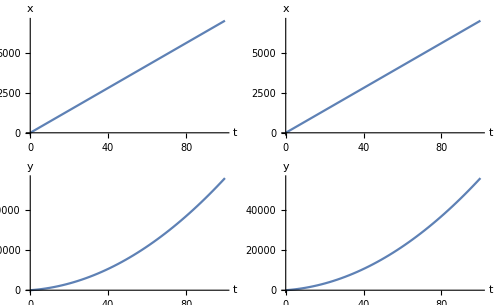

```mathematica
GraphicsGrid[{{Plot[xx[t],{t,0,100},AxesLabel->{t,x}],Plot[vx0OptAng[[2]]*t,{t,0,100},AxesLabel->{t,x}]},{Plot[yy[t],{t,0,100},AxesLabel->{t,y}],Plot[vy0OptAng[[2]]*t-1/2*(g)*t^2,{t,0,100},AxesLabel->{t,y}]}},Frame->All]
```

We can see from the plots above that the integrated equations of motion without drag are correct.

```mathematica
xt[x0_,θ_,t_]:=x0+vx0[v0OptAng,θ]*t
```

```mathematica
yt[y0_,θ_,t_]:=y0+vy0[v0OptAng,θ]*t+1/2*g*t^2
```

```mathematica
xy=Table[{(xt[0,θ,t])[[2]],(yt[0,θ,t])[[2]]},{θ,π/12,(5π)/12,π/12}]
```

{{95.6218 t,25.6218 t-4.9 t^2},{85.7321 t,49.4975 t-4.9 t^2},{70. t,70. t-4.9 t^2},{49.4975 t,85.7321 t-4.9 t^2},{25.6218 t,95.6218 t-4.9 t^2}}

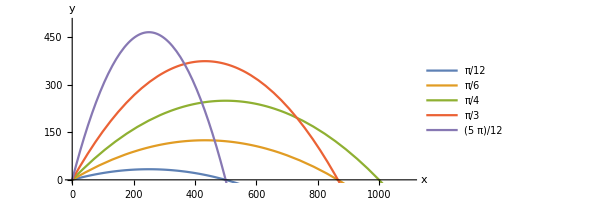

```mathematica
ParametricPlot[{{95.6217782649107*t,25.621778264910702*t-4.9* t^2},{85.73214099741125*t,49.497474683058336*t-4.9* t^2},{70 *t,70*t-4.9* t^2},{49.497474683058336*t,85.73214099741125* t-4.9* t^2},{25.621778264910702*t,95.6217782649107* t-4.9* t^2}},{t,0,25},PlotRange->{{0,1100},{0,500}},PlotLegends->{π/12,π/6,π/4,π/3,(5π)/12},AxesLabel->{x,y}]
```

## Problem 3

A (frontal area) is best defined by r^2/2

```mathematica
v=√((xDrag'[T])^2+(yDrag'[T])^2)
```

√(xDrag'[T]^2+yDrag'[T]^2)

```mathematica
fDrag[ρ_,r_,v_]=-ρ*(r^2/2)*v^2
```

-1/2 r^2 ρ (xDrag'[T]^2+yDrag'[T]^2)

```mathematica
eqsDrag[ρ_,r_,m_]:={xDrag''[T]==(-Abs[fDrag[ρ,r,v]])/m*xDrag'[T]/v,yDrag''[T]==g+(-Abs[fDrag[ρ,r,v]])/m*yDrag'[T]/v}
```

```mathematica
iniDrag[v0_,θ_]:={xDrag[0]==0,yDrag[0]==0,xDrag'[0]==vx0[v0,θ],yDrag'[0]==vy0[v0,θ]}
```

```mathematica
rulesDrag[T_,ρ_,r_,m_,v0_,θ_]:=NDSolve[Join[eqsDrag[ρ1,r1,m1]/.{ρ1-> ρ,r1->r,m1->m},iniDrag[v01,θ1]]/.{v01-> v0,θ1->θ},{xDrag[T],yDrag[T]},{T,0,1000}]
```

```mathematica
xxDrag[t_,ρ_,r_,m_,v0_,θ_]:=(xDrag[T]/.((rulesDrag[T,ρ,r,m,v0,θ])[[1]]))/.T-> t
```

```mathematica
yyDrag[t_,ρ_,r_,m_,v0_,θ_]:=(yDrag[T]/.((rulesDrag[T,ρ,r,m,v0,θ])[[1]]))/.T->t
```

```mathematica
trajectory={xxDrag[t,1.3,0.05,0.5,99.89,π/4],yyDrag[t,1.3,0.05,0.5,99.89,π/4]}
```

{InterpolatingFunction[{{0., 1000.}}, <>][t],InterpolatingFunction[{{0., 1000.}}, <>][t]}

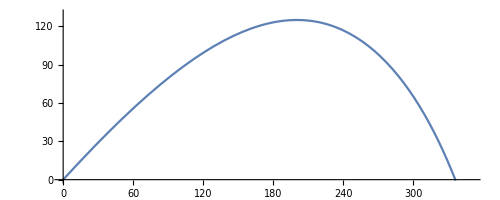

```mathematica
ParametricPlot[trajectory,{t,0,10},PlotRange->{{0,350},{0,130}}]
```

## Problem 4

```mathematica
trajectories={{xxDrag[t,1.3,0.05,0.5,1100,π/24],yyDrag[t,1.3,0.05,0.5,1100,π/24]},{xxDrag[t,1.3,0.05,0.5,850,π/12],yyDrag[t,1.3,0.05,0.5,850,π/12]},{xxDrag[t,1.3,0.05,0.5,800,π/6],yyDrag[t,1.3,0.05,0.5,800,π/6]},{xxDrag[t,1.3,0.05,0.5,1350,π/4],yyDrag[t,1.3,0.05,0.5,1350,π/4]},{xxDrag[t,1.3,0.05,0.5,6500,π/3],yyDrag[t,1.3,0.05,0.5,6500,π/3]}};
```

You can use ParametricPlot[trajectories,{t,0,100},PlotRange→{{0,1100},{0,1400}},AxesLabel→{x,y}]
to plot the trajectories instead of the cell below. This way is much faster, but the trajectories won’t be color coded.

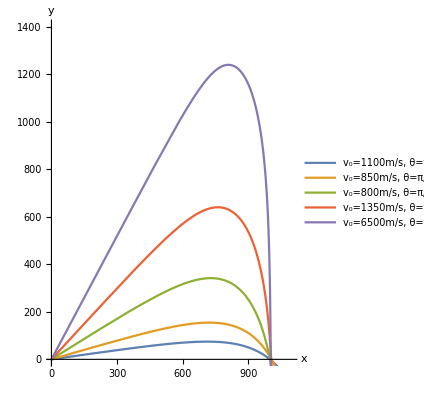

```mathematica
trajsPlot=ParametricPlot[{{xxDrag[t,1.3,0.05,0.5,1100,π/24],yyDrag[t,1.3,0.05,0.5,1100,π/24]},{xxDrag[t,1.3,0.05,0.5,850,π/12],yyDrag[t,1.3,0.05,0.5,850,π/12]},{xxDrag[t,1.3,0.05,0.5,800,π/6],yyDrag[t,1.3,0.05,0.5,800,π/6]},{xxDrag[t,1.3,0.05,0.5,1350,π/4],yyDrag[t,1.3,0.05,0.5,1350,π/4]},{xxDrag[t,1.3,0.05,0.5,6500,π/3],yyDrag[t,1.3,0.05,0.5,6500,π/3]}},{t,0,100},PlotRange->{{0,1100},{0,1400}},PlotLegends->{"v_0=1100m/s, θ=π/24rad","v_0=850m/s, θ=π/12rad","v_0=800m/s, θ=π/6rad","v_0=1350m/s, θ=π/4rad","v_0=6500m/s, θ=π/3rad"},AxesLabel->{x,y}]
```

## Problem 5

### (a)

```mathematica
landingTime[ρ_,r_,m_,v0_,θ_]:=t/.(FindRoot[yyDrag[t,ρ,r,m,v0,θ]==0,{t,(2*v0*Sin[θ])/-g}])[[1]]
```

### (b)

```mathematica
xLanding[ρ_,r_,m_,v0_,θ_]:=(xxDrag[(landingTime[ρ,r,m,v0,θ]),ρ,r,m,v0,θ])
```

### (c)

```mathematica
findInitVel[ρ_,r_,m_,θ_,x_]:=Module[{v0=0.1},While[xLanding[ρ,r,m,v0,θ]<x,v0=v0+1000];v0=v0-1000;
While[xLanding[ρ,r,m,v0,θ]<x,v0=v0+100];v0=v0-100;
While[xLanding[ρ,r,m,v0,θ]<x,v0=v0+10];v0=v0-10;
While[xLanding[ρ,r,m,v0,θ]<x,v0=v0+1];v0=v0-1;
While[xLanding[ρ,r,m,v0,θ]<x,v0=v0+0.1];v0=v0-0.1;
v0]
```

At θ = π/4 and a range of 1000m

```mathematica
findInitVel[1.3,0.05,0.5,π/4,1000]
```

1321.2

The initial velocity is 1321.2 m/s.

### (d)

```mathematica
findOptAng[ρ_,r_,m_,x_]:=Module[{θ=π/180},While[findInitVel[ρ,r,m,θ+π/45,x]<findInitVel[ρ,r,m,θ,x],θ=θ+π/45];θ=θ-π/45;While[findInitVel[ρ,r,m,θ+π/180,x]<findInitVel[ρ,r,m,θ,x],θ=θ+π/180];θ=θ-π/180;θ]
```

```mathematica
180/π findOptAng[1.3,0.05,0.5,1000]
```

23

The angle with the least initial velocity required to reach PCC is 23°